# Solución de la ecuación de difusión de calor no homogénea bidimensional por medio de diferencias finitas (Crank-Nicolson method).

## Inicialización y declaración de variables y parámetros

```mathematica
Clear[f];
Clear[n];
Clear[ρ];
Clear[h];
Clear[μ];
Clear[γ]
Clear[MCN];
Clear[FV];
Clear[SV];

(*fl es la frecuencia del laser*)
fl=54*10^6;
(*NpP son los nodos TEMPORALES por pulso láser*)
NpP=3;
Δt=(1/fl)/NpP;
N[Δt]
(*alpha es la difusividad térmica en METROS cuadrados sobre SEGUNDO. k es la conductividad térmica en Watts sobre metro grado kelvin. mu, ro y gamma simplifican la sintaxis de la ecuación de Crank-Nicolson y el método funciona bien para mu<1, muy bien para mu<1/2*)
α=54.3*10^-6;
k=138;
(*Magic step √(2*α*Δt)*)
Δx=5*10^-6
μ=α*Δt/((Δx)^2)
ρ=μ/(2+(4*μ));
γ=(1-(2*μ))/(1+(2*μ));
```

6.17284×10^-9

1/200000

0.0134074

```mathematica
(*TSS1D (total spatial steps in 1D) es el número de nodos lineales en la simulación. Toma en cuenta los nodos frontera (cero y longitud máxima). Este código asumira por facilidad un grid con igual separación X/Y por paso y también iguales dimensiones totales (grid cuadrada). El número total de nodos a calcular por paso TEMPORAL es de (TSS1D-2)^2  TTS es el número total de pasos TEMPORALES de la simulación.*)
TSS1D=40;
TTS=500;

(*Condición inicial, esta es una función de x_ y y_.
Tinf es la temperatura inicial,también se considera esta temperatura como temperatura en el infinito *)
Tinf=20;
f[0,x_,y_]=f[0.,x_,y_]=Tinf;

(*Condiciones de frontera fijas e iguales a Tinf.*)

f[t_,0,y_]=Tinf;
f[t_,x_,0]=Tinf;
f[t_,TSS1D-1,y_]=Tinf;
f[t_,x_,TSS1D-1]=Tinf;



(*h es el término de generación de calor. La función IF hace que h tenga valores sólo cuando el argumento IntegerQ es verdadero. BW es el ancho ESPACIAL del pulso láser. FLU es la fluencia del pulso láser en J/m2*)

BW=20*10^-6;
FLU=10;
ABS=50*10^6;

h:=If[IntegerQ[#1/3],(1-0.69)*(α/k)*((2*FLU/Δt)/(Pi*(BW/Δx)^2)*Exp[-2*((#2-(TSS1D-1)/2)^2+(#3-(TSS1D-1)/2)^2)/(BW/Δx)^2]),0]&

(*VISUALIZACIÓN DEL TREN DE PULSOS*)

(*Manipulate[Plot3D[h[t,x,y],{x,0,TSS1D-1},{y,0,TSS1D-1},PlotRange->All],{t,0,TTS,1}]*)


(*Matrix del método Crank Nicolson.*)
MCN=SparseArray[{{i_,i_}->1,{i_,j_}/;Abs[i-j]==TSS1D-2->-ρ,Band[{1,2}]->Table[If[Divisible[i,TSS1D-2],0,-ρ],{i,(TSS1D-2)^2-1}],Band[{2,1}]->Table[If[Divisible[i,TSS1D-2],0,-ρ],{i,(TSS1D-2)^2-1}]},{(TSS1D-2)^2,(TSS1D-2)^2}];


(*FV es una función para generar los elementos del vector de soluciónes. SV es el Vector de soluciones del método Crank Nicolson*)
FV=ρ*(f[#1-1,#2,#3-1]+f[#1-1,#2,#3+1]+f[#1-1,#2-1,#3]+f[#1-1,#2+1,#3])+γ*f[#1-1,#2,#3]+(1/(1+2*μ)*h[#1,#2,#3])+(ρ*Tinf*(Piecewise[{{2,#2==1&&#3==1},{2,#2==1&&#3==TSS1D-2},{1,#2==1&&1<#3<TSS1D-2},{2,#2==TSS1D-2&&#3==1},{2,#2==TSS1D-2&&#3==TSS1D-2},{1,#2==TSS1D-2&&1<#3<TSS1D-2},{1,1<#2<TSS1D-2&&#3==1},{1,1<#2<TSS1D-2&&#3==TSS1D-2}},0]))&;

SV=Flatten[Table[FV[#1,i,j],{i,1,TSS1D-2},{j,1,TSS1D-2}]]&;
```

## Rutina Crank-Nicolson

```mathematica
RM=Table[(Table[f[n,x,y]=LinearSolve[MCN,SV[n]][[((TSS1D-2)*(x-1))+y]],{x,1,TSS1D-2},{y,1,TSS1D-2}]),{n,1,TTS,1}];
```

## Visualización

```mathematica
Manipulate[ListPointPlot3D[Flatten[Table[{Δx*x,Δx*y,f[n,x,y]},{x,0,TSS1D-1},{y,0,TSS1D-1}],1],PlotRange->{{0,(TSS1D-1)*Δx},{0,(TSS1D-1)*Δx},{20,585}}],{n,0,TTS,1}]
```

```mathematica
N[Δt*TTS]
```

3.08642×10^-6

```mathematica
f[TTS,1,1]
```

20.

```mathematica
Max[RM[[-1]]]
```

580.16

```mathematica
SetDirectory["C:\\Users\\Natanael\\Desktop\\calor"];
```

```mathematica
RM>>"MoΔx5umΔt6nsFLU10Jm2BW20um"
```

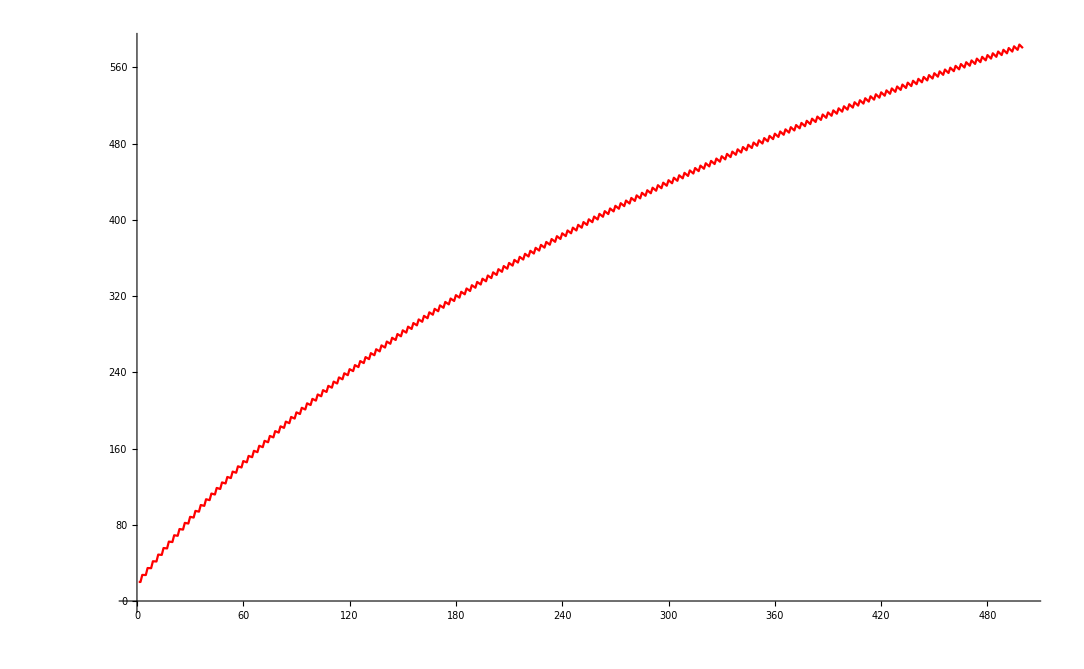

```mathematica
ListPlot[Table[RM[[t]][[(TSS1D)/2]][[(TSS1D)/2]],{t,1,TTS}],PlotStyle->{Red,PointSize[Small]},Joined->True]
```

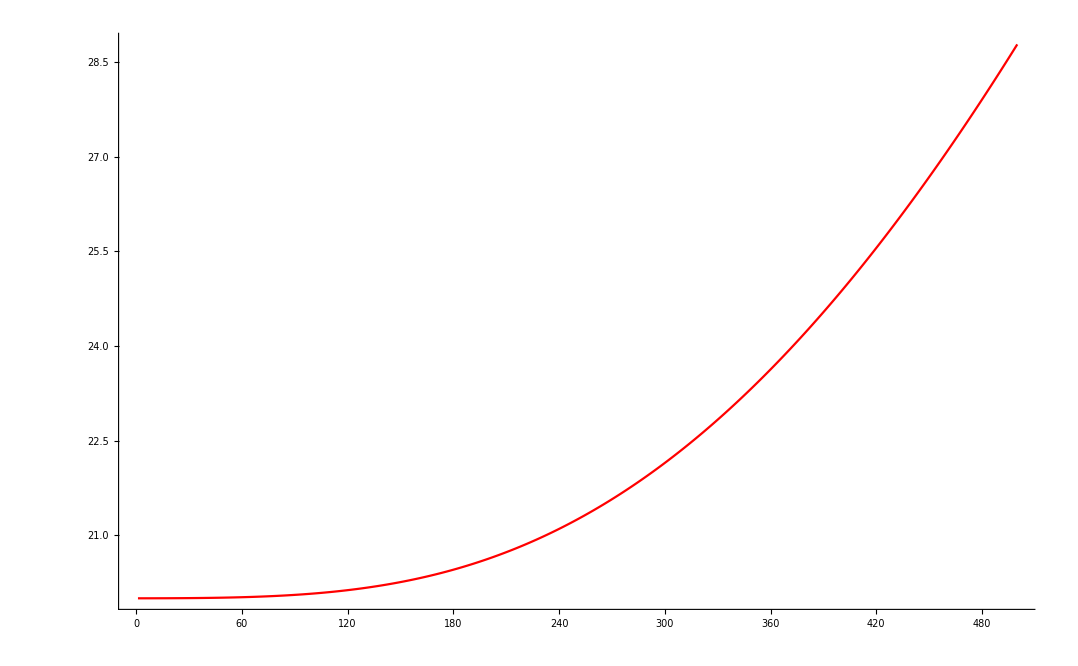

```mathematica
ListPlot[Table[RM[[t]][[(TSS1D)/4]][[(TSS1D)/2]],{t,1,TTS}],PlotStyle->{Red,PointSize[Small]},Joined->True]
```